In this notebook, we derive the dynamical equations describing the growth of a lumen made of two (symmetric or asymmetric) spherical caps.

The notebook has been divided into two sections (“Symmetric spherical cap” and “Spherical cap with two non-symmetric lumen”), themselves divided into subsections to simplify its reading and evaluation.
The two sections are independent.
It is  however recommended to first evaluate first the “Symmetric spherical cap” section, as some equations derived in this first section are used in the second one for a sanity check (not evaluating the first section is however not critical : the check will simply fail) 

At the end of section “Spherical cap with two non-symmetric lumen”, we show how to reproduce the asymmetric lumen figure of the manuscript.

## Symmetric spherical cap

### Equations and dimensionless form

#### Transport equations and force balance

```mathematica
ionConservation=-NN'[t]+(-Λ ΔC[t]+Jp)As[t]-Ps[t] jP/(L-R[t]Sin[θ[t]])
solNN=Solve[%==0,NN'[t]]//Simplify//Flatten
```

-(jP Ps[t])/(L-R[t] Sin[θ[t]])+As[t] (Jp-Λ ΔC[t])-NN'[t]

{NN'[t]→-(jP Ps[t])/(L-R[t] Sin[θ[t]])+As[t] (Jp-Λ ΔC[t])}

```mathematica
concentrationDef=-ΔC'[t]+1/Vs[t](NN'[t]-(Ccell+ΔC[t])Vs'[t])
```

(NN'[t]-(Ccell+ΔC[t]) Vs'[t])/Vs[t]-ΔC'[t]

```mathematica
-Vs'[t]+(Λw (ΔP-ΔΠ)+Jw)As[t]- Ps[t] jPw/(L-R[t]Sin[θ[t]])/.ΔΠ-> -kB T ΔC[t];
volumeConservation =%
```

-(jPw Ps[t])/(L-R[t] Sin[θ[t]])+As[t] (Jw+Λw (ΔP+kB T ΔC[t]))-Vs'[t]

```mathematica
solPressure=Solve[-ΔP-(2Γ)/R[t]==0,ΔP]//Flatten
```

{ΔP→-(2 Γ)/R[t]}

```mathematica
YoungDupre=Γ Cos[θ[t]]-γj-σr/(R[t]Sin[θ[t]])
```

-γj+Γ Cos[θ[t]]-(σr Csc[θ[t]])/R[t]

#### Spherical cap geometry

```mathematica
repTimeDep={R->R[t],θ->θ[t]};
VsphericalCap=(2π)/3 R^3(2+Cos[θ])(1-Cos[θ])^2;
AsphericalCap=4π R^2(1-Cos[θ]);
PsphericalCap=2π R Sin[θ];
```

```mathematica
VsphericalCap/.repTimeDep
D[%,t];
Collect[%,{θ'[t],R'[t]},Simplify]
```

2/3 π (1-Cos[θ[t]])^2 (2+Cos[θ[t]]) R[t]^3

2 π (-1+Cos[θ[t]])^2 (2+Cos[θ[t]]) R[t]^2 R'[t]+2 π R[t]^3 Sin[θ[t]]^3 θ'[t]

```mathematica
{PsphericalCap,AsphericalCap,VsphericalCap}/.repTimeDep/.repLinearStab;
Series[%,{ϵ,0,1}]//Normal;
Coefficient[%,ϵ];
Collect[%,f_[t],FullSimplify]
```

ReplaceAll::reps: {repLinearStab} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

0

#### Dimensionless equations

```mathematica
repDimlessVariables={R->(r[#/T0] R0&),ΔC->(Δc[#/T0]C0 &),θ-> (α[#/T0]&),Vs->(vs[#/T0] V0&),As->(as[#/T0] A0&),Ps->(ps[#/T0] P0&),t->tt T0};
repGeometry={V0->4/3 π R0^3,A0->4π R0^2,P0->2π R0};
```

```mathematica
{(C0 kB T T0 Λw)/R0==1,C0 ccell==Ccell,(T0 Λ)/R0==1,R0==L,(*(T0 Γ Λw)/R0^2==1,*)(Jp T0)/(C0 R0)==jp,(Jw T0)/R0==jw,(jP T0)/(C0 R0^3)==jjP,(jPw T0)/R0^3==jjPw,γj/Γ==γγj,σr/(R0 Γ)==σσr,(Γ Λw)/(L Λ)==γ};
repDimlessParameters=Solve[%,{C0,T0,R0,Jp,Jw,jP,jPw,γj,σr,Ccell,Γ}]//Flatten
repDimlessToDimfull=Solve[%%,{C0,T0,R0,jp,jw,jjP,jjPw,γγj,σσr,ccell,γ}]//Flatten
```

{C0→Λ/(kB T Λw),T0→L/Λ,R0→L,Jp→(jp Λ^2)/(kB T Λw),Jw→jw Λ,jP→(jjP L^2 Λ^2)/(kB T Λw),jPw→jjPw L^2 Λ,γj→(L γ γγj Λ)/Λw,σr→(L^2 γ Λ σσr)/Λw,Ccell→(ccell Λ)/(kB T Λw),Γ→(L γ Λ)/Λw}

{C0→Λ/(kB T Λw),T0→L/Λ,R0→L,jp→(Jp kB T Λw)/Λ^2,jw→Jw/Λ,jjP→(jP kB T Λw)/(L^2 Λ^2),jjPw→jPw/(L^2 Λ),γγj→γj/Γ,σσr→σr/(L Γ),ccell→(Ccell kB T Λw)/Λ,γ→(Γ Λw)/(L Λ)}

```mathematica
T0/V0 volumeConservation/.solPressure/.repDimlessVariables/.repGeometry/.repDimlessParameters//Expand//Simplify;
eq1=Collect[%,{Δc'[tt],vs'[tt],ps[tt],as[tt],Δc[tt],r[tt]},FullSimplify]
```

(3 jjPw ps[tt])/(-2+2 r[tt] Sin[α[tt]])+3 as[tt] (jw-(2 γ)/r[tt]+Δc[tt])-vs'[tt]

```mathematica
T0/C0 concentrationDef/.solNN/.repDimlessVariables/.repGeometry/.repDimlessParameters//Expand//Simplify;
eq2=Collect[%,{Δc'[tt],vs'[tt],ps[tt],as[tt],Δc[tt]},Simplify]
```

(3 jjP ps[tt])/(-2 vs[tt]+2 r[tt] Sin[α[tt]] vs[tt])+as[tt] ((3 jp)/vs[tt]-(3 Δc[tt])/vs[tt])+(-ccell/vs[tt]-Δc[tt]/vs[tt]) vs'[tt]-Δc'[tt]

```mathematica
YoungDupre/Γ/.repDimlessVariables/.repGeometry/.repDimlessParameters;
eq3=Collect[%,{Δc'[tt],vs'[tt],ps[tt],as[tt],Δc[tt]},Simplify]
```

-γγj+Cos[α[tt]]-(σσr Csc[α[tt]])/r[tt]

```mathematica
geomDimlessTemp={VsphericalCap/V0,AsphericalCap/A0,PsphericalCap/P0}/.repTimeDep/.repDimlessVariables/.repGeometry
repGeomDimless={vs->(geomDimlessTemp[[1]]/.tt->#&),as->(geomDimlessTemp[[2]]/.tt->#&),ps->(geomDimlessTemp[[3]]/.tt->#&)}
```

{1/2 (1-Cos[α[tt]])^2 (2+Cos[α[tt]]) r[tt]^3,(1-Cos[α[tt]]) r[tt]^2,r[tt] Sin[α[tt]]}

{vs→(geomDimlessTemp⟦1⟧/.tt→#1&),as→(geomDimlessTemp⟦2⟧/.tt→#1&),ps→(geomDimlessTemp⟦3⟧/.tt→#1&)}

### Steady-state and linear stab analysis

#### Dimensionless equations at steady-state

```mathematica
repSteadyState={vs->(vs&),as->(as&),ps->(ps&),r->(r&),Δc->(Δc&),α->(α&),ρρ->(ρρ&)}
```

{vs→(vs&),as→(as&),ps→(ps&),r→(r&),Δc→(Δc&),α→(α&),ρρ→(ρρ&)}

```mathematica
eqSteadyState={eq1,eq2,eq3}/.repSteadyState
```

{3 as (jw-(2 γ)/r+Δc)+(3 jjPw ps)/(-2+2 r Sin[α]),as ((3 jp)/vs-(3 Δc)/vs)+(3 jjP ps)/(-2 vs+2 r vs Sin[α]),-γγj+Cos[α]-(σσr Csc[α])/r}

```mathematica
geomDimlessSteadyStateTemp={VsphericalCap/V0,AsphericalCap/A0,PsphericalCap/P0}/.repTimeDep/.repDimlessVariables/.repGeometry/.repSteadyState
repGeomDimlessSteadyState={vs->geomDimlessSteadyStateTemp[[1]],as->geomDimlessSteadyStateTemp[[2]],ps->geomDimlessSteadyStateTemp[[3]]}
```

{1/2 r^3 (1-Cos[α])^2 (2+Cos[α]),r^2 (1-Cos[α]),r Sin[α]}

{vs→1/2 r^3 (1-Cos[α])^2 (2+Cos[α]),as→r^2 (1-Cos[α]),ps→r Sin[α]}

#### Equations for linear stability analysis dimensionless

```mathematica
repLinearStabDimless={ Δc->(Δc+ϵ δc[#]&),r->(r+ϵ δr[#]&),α->(α+ϵ δα[#]&),as->(as+ϵ δa[#]&),vs->(vs+ϵ δv[#]&),ps->(ps+ϵ δp[#]&)}
vars={δr[tt],δc[tt],δα[tt]};
```

{Δc→(Δc+ϵ δc[#1]&),r→(r+ϵ δr[#1]&),α→(α+ϵ δα[#1]&),as→(as+ϵ δa[#1]&),vs→(vs+ϵ δv[#1]&),ps→(ps+ϵ δp[#1]&)}

```mathematica
{VsphericalCap/V0,AsphericalCap/A0,PsphericalCap/P0}/.repTimeDep/.repDimlessVariables/.repGeometry;
%/.repLinearStabDimless;
Series[%,{ϵ,0,1}]//Normal;
coefs=Coefficient[%,ϵ]
repGeomDimlessPerturbed={δv->Evaluate@(coefs[[1]]/.tt->#&),δa->Evaluate@(coefs[[2]]/.tt->#&),δp->Evaluate@(coefs[[3]]/.tt->#&)}
```

{-3/2 (-2 r^2 δr[tt]+3 r^2 Cos[α] δr[tt]-r^2 Cos[α]^3 δr[tt]-r^3 Sin[α] δα[tt]+r^3 Cos[α]^2 Sin[α] δα[tt]),2 r (1-Cos[α]) δr[tt]+r^2 Sin[α] δα[tt],Sin[α] δr[tt]+r Cos[α] δα[tt]}

{δv→(coefs⟦1⟧/.tt→#1&),δa→(coefs⟦2⟧/.tt→#1&),δp→(coefs⟦3⟧/.tt→#1&)}

```mathematica
eq3/.repLinearStabDimless;
Series[%,{ϵ,0,1}]//Normal;
Coefficient[%,ϵ];
%/.repGeomDimlessPerturbed/.repGeomDimlessSteadyState//Simplify
solTemp=Solve[%==0,δα[tt]]//Flatten
solAlpha={δα-> (δα[tt]/.solTemp/.tt-># &)}
```

-Sin[α] δα[tt]+(σσr Csc[α] (δr[tt]+r Cot[α] δα[tt]))/r^2

{δα[tt]→(σσr Csc[α]^2 δr[tt])/(r (r-σσr Cot[α] Csc[α]^2))}

{δα→(δα[tt]/.solTemp/.tt→#1&)}

```mathematica
{eq1,eq2}/.repLinearStabDimless;
Series[%,{ϵ,0,1}]//Normal;
Coefficient[%,ϵ];
%/.repGeomDimlessPerturbed/.repGeomDimlessSteadyState//Simplify;
eqLinearStabNoAlpha=%/.solAlpha//Simplify;
solLinearStabNoAlpha=Solve[%==0,D[vars[[1;;2]],tt]]//Flatten//Simplify;
```

```mathematica
MstabNoAlpha = Table[
Coefficient[i/.solLinearStabNoAlpha,j]
,{i,D[vars[[1;;2]],tt] },{j,vars[[1;;2]]}
]//Simplify;
```

```mathematica
(* check*)
(D[vars[[1;;2]],tt]/.solLinearStabNoAlpha)-MstabNoAlpha.vars[[1;;2]]//Simplify
```

{0,0}

```mathematica
(* example of steady-state solution and corresponding eigenvalues *)
repParams={jp->4.5,jw->0.017,jjP->0.87,jjPw->0.63,γγj->1.,σσr->-0.16,ccell->0.01,γ->0.00017}
eqExplicit=eqSteadyState/.repGeomDimlessSteadyState/.repParams;
solExplicit=Solve[eqExplicit==0&&0<=α<=π&&r>0,{r,Δc,α},Reals]//N
eigExplicit=Table[MstabNoAlpha/.repParams/.solExplicit[[i]]//N//Eigenvalues,{i,1,Length@solExplicit}]
```

{jp→4.5,jw→0.017,jjP→0.87,jjPw→0.63,γγj→1.,σσr→-0.16,ccell→0.01,γ→0.00017}

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{r→0.125173,Δc→1.88172,α→1.96598}}

{{2752.27,-51.2341}}

## Spherical cap with two non-symmetric lumen

### Equations

#### Spherical cap geometry

```mathematica
repTimeDep={R->R[t],θ->θ[t]};
repDimlessVariables={R->(r[#/T0] R0&),ΔC->(Δc[#/T0]C0 &),θ-> (α[#/T0]&),Vs->(vs[#/T0] V0&),As->(as[#/T0] A0&),Ps->(ps[#/T0] P0&),t->tt T0};
repGeometry={V0->4/3 π R0^3,A0->4π R0^2,P0->2π R0};
```

```mathematica
VsphericalCap=(2π)/3 R^3(2+Cos[θ])(1-Cos[θ])^2;
AsphericalCap=4π R^2(1-Cos[θ]);
PsphericalCap=2π R Sin[θ];
```

```mathematica
geomDimlessTemp={VsphericalCap/V0,AsphericalCap/A0,PsphericalCap/P0}/.repTimeDep/.repDimlessVariables/.repGeometry
repGeomDimless={vs->(geomDimlessTemp[[1]]/.tt->#&),as->(geomDimlessTemp[[2]]/.tt->#&),ps->(geomDimlessTemp[[3]]/.tt->#&)}
```

{1/2 (1-Cos[α[tt]])^2 (2+Cos[α[tt]]) r[tt]^3,(1-Cos[α[tt]]) r[tt]^2,r[tt] Sin[α[tt]]}

{vs→(geomDimlessTemp⟦1⟧/.tt→#1&),as→(geomDimlessTemp⟦2⟧/.tt→#1&),ps→(geomDimlessTemp⟦3⟧/.tt→#1&)}

#### Full equations (and check with symmetric case)

```mathematica
repCheckAsymToSym={α[i_]->α,R[i_]->R,ΔC[i_]->Δc,r[i_]->r,Δc[i_]->Δc,Γ[i_]->Γ,Ccell[i_]->Ccell,ηb[i_]->0};
repSimple={Λw[i_]->Λw,Jw[i_]->Jw,Λ[i_]->Λ,Jp[i_]->Jp(*,ηb[i_]->ηb*)};
repDimless={R->r,ΔC->Δc,t->tt,R0->1,Λw->1,kB->1,T->1,Γ->γ,Λ->1,Jw->jw,Jp->jp,jPw->jjPw,jP->jjP,γj->γγj,σr->σσr,L->1,Ccell->ccell};
repPressure={ΔP[i_]->-(2 Γ[i])/(R[i][t])-4ηb[i] (R[i]'[t])/(R[i][t])^2};(*normal force balance*)
```

```mathematica
geomDimless={1/2 vs[tt],1/2 as[tt],ps[tt]}/.repGeomDimless (* we divide by two because those were twice the volume and area of a spherical cap *)
repGeomDimlessAsym={vs->((geomDimless[[1]]/.α->α[1]/.r->r[1])+(geomDimless[[1]]/.α->α[2]/.r->r[2])/.tt->#&),as[i_]->(geomDimless[[2]]/.α->α[i]/.r->r[i]/.tt->#&),ps->(geomDimless[[3]]/.α->α[1]/.r->r[1]/.tt->#&)};
```

{1/4 (1-Cos[α[tt]])^2 (2+Cos[α[tt]]) r[tt]^3,1/2 (1-Cos[α[tt]]) r[tt]^2,r[tt] Sin[α[tt]]}

```mathematica
volumeConservationAssym=-(jPw Ps[t])/(L-R0 r[1][t] Sin[α[1][t]])-Vs'[t]+Sum[As[i][t] (Jw[i]+Λw[i] (ΔP[i]+kB T ΔC[i][t])),{i,1,2}]
```

-(jPw Ps[t])/(L-R0 Sin[α[1][t]] r[1][t])+As[1][t] (Jw[1]+Λw[1] (ΔP[1]+kB T ΔC[1][t]))+As[2][t] (Jw[2]+Λw[2] (ΔP[2]+kB T ΔC[2][t]))-Vs'[t]

```mathematica
volumeConservationAssym/V0/.ΔP[2]->ΔP[1];(*pressure in both cells are equal (mechanical eq)*)
%/.repPressure;(*normal force balance*)
volumeConservationAssymDimless=%/.{As[i_]->(A0 as[i][#]&),Ps->(P0 ps[#]&),Vs->(V0 vs[#]&)}/.repGeometry//Simplify
volumeConservationAssymDimlessOnlyR=%/.repGeomDimlessAsym
```

(3 jPw ps[t])/(2 R0^2 (-L+R0 Sin[α[1][t]] r[1][t]))-vs'[t]+(3 as[1][t] (Jw[1]+Λw[1] (-(2 Γ[1])/(R[1][t])+kB T ΔC[1][t]-(4 ηb[1] R[1]'[t])/(R[1][t])^2)))/R0+(3 as[2][t] (Jw[2]+Λw[2] (-(2 Γ[1])/(R[1][t])+kB T ΔC[2][t]-(4 ηb[1] R[1]'[t])/(R[1][t])^2)))/R0

(3 jPw Sin[α[1][t]] r[1][t])/(2 R0^2 (-L+R0 Sin[α[1][t]] r[1][t]))-3/4 (1-Cos[α[1][t]])^2 (2+Cos[α[1][t]]) (r[1][t])^2 r[1]'[t]-3/4 (1-Cos[α[2][t]])^2 (2+Cos[α[2][t]]) (r[2][t])^2 r[2]'[t]+(3 (1-Cos[α[1][t]]) (r[1][t])^2 (Jw[1]+Λw[1] (-(2 Γ[1])/(R[1][t])+kB T ΔC[1][t]-(4 ηb[1] R[1]'[t])/(R[1][t])^2)))/(2 R0)+(3 (1-Cos[α[2][t]]) (r[2][t])^2 (Jw[2]+Λw[2] (-(2 Γ[1])/(R[1][t])+kB T ΔC[2][t]-(4 ηb[1] R[1]'[t])/(R[1][t])^2)))/(2 R0)+1/4 (1-Cos[α[1][t]])^2 Sin[α[1][t]] (r[1][t])^3 α[1]'[t]-1/2 (1-Cos[α[1][t]]) (2+Cos[α[1][t]]) Sin[α[1][t]] (r[1][t])^3 α[1]'[t]+1/4 (1-Cos[α[2][t]])^2 Sin[α[2][t]] (r[2][t])^3 α[2]'[t]-1/2 (1-Cos[α[2][t]]) (2+Cos[α[2][t]]) Sin[α[2][t]] (r[2][t])^3 α[2]'[t]

```mathematica
(*check that we recover the symmetric case *)
checkVol=volumeConservationAssymDimlessOnlyR/.repCheckAsymToSym/.repSimple/.repDimless;
(eq1/.repGeomDimless)-checkVol//Simplify
```

eq1+r[tt] (6 γ-6 γ Cos[α[tt]]+(3 jjPw Sin[α[tt]])/(2-2 r[tt] Sin[α[tt]]))-3/2 r[tt]^2 Sin[α[tt]/2]^2 (4 jw+4 Δc[tt]+(-3+2 Cos[α[tt]]+Cos[2 α[tt]]) r'[tt])+3/2 r[tt]^3 Sin[α[tt]]^3 α'[tt]

```mathematica
ionConservationAssym=-NN'[t]+Sum[As[i][t] (Jp[i]-Λ[i] ΔC[i][t]),{i,1,2}]- Ps[t] jP/(L-R0 r[1][t]Sin[α[1][t]]);
solNNAssym=Solve[%==0,NN'[t]]//Simplify//Flatten
```

{NN'[t]→-(jP Ps[t])/(L-R0 Sin[α[1][t]] r[1][t])+As[1][t] (Jp[1]-Λ[1] ΔC[1][t])+As[2][t] (Jp[2]-Λ[2] ΔC[2][t])}

```mathematica
Table[
concentration[i]=-ΔC[i]'[t]+NN'[t]/Vs[t]-(Ccell[i]+ΔC[i][t])Vs'[t]/Vs[t]/.solNNAssym;
concentrationAssymDimless[i]=concentration[i]/.{As[i_]->(A0 as[i][#]&),Ps->(P0 ps[#]&),Vs->(V0 vs[#]&)}/.repGeometry//Simplify;
concentrationAssymDimlessOnlyR[i]=concentrationAssymDimless[i]/.repGeomDimlessAsym;
,{i,1,2}];
Table[
checkCon[i]=concentrationAssymDimlessOnlyR[i]/.repCheckAsymToSym/.repSimple/.repDimless
,{i,1,2}];
```

```mathematica
(*check that we recover the symmetric case *)
(eq2/.repGeomDimless)-checkCon[2]//Simplify
```

eq2-(3 ((jjP Sin[α[tt]])/(-1+r[tt] Sin[α[tt]])-2 (-1+Cos[α[tt]]) r[tt] (jp-Δc[tt])))/((-1+Cos[α[tt]])^2 (2+Cos[α[tt]]) r[tt]^2)+(3 (ccell+Δc[tt]) ((-2+Cos[α[tt]]+Cos[α[tt]]^2) r'[tt]-(1+Cos[α[tt]]) r[tt] Sin[α[tt]] α'[tt]))/((-1+Cos[α[tt]]) (2+Cos[α[tt]]) r[tt])+Δc'[tt]

```mathematica
concentrationAssymDimlessOnlyR[2]-concentrationAssymDimlessOnlyR[1]/.ΔC[2]->(Ccell[1]-Ccell[2]+ΔC[1][#]&)//Simplify
```

0

```mathematica
volumeConservationAssymDimlessOnlyR/.repSimple/.Γ->γ;
volumeConservationAssymDimlessOnlyRSimple=%/.repDimless
```

(3 jjPw Sin[α[1][tt]] r[1][tt])/(2 (-1+Sin[α[1][tt]] r[1][tt]))-3/4 (1-Cos[α[1][tt]])^2 (2+Cos[α[1][tt]]) (r[1][tt])^2 r[1]'[tt]+3/2 (1-Cos[α[1][tt]]) (r[1][tt])^2 (jw-(2 γ[1])/(r[1][tt])+Δc[1][tt]-(4 ηb[1] r[1]'[tt])/(r[1][tt])^2)+3/2 (1-Cos[α[2][tt]]) (r[2][tt])^2 (jw-(2 γ[1])/(r[1][tt])+Δc[2][tt]-(4 ηb[1] r[1]'[tt])/(r[1][tt])^2)-3/4 (1-Cos[α[2][tt]])^2 (2+Cos[α[2][tt]]) (r[2][tt])^2 r[2]'[tt]+1/4 (1-Cos[α[1][tt]])^2 Sin[α[1][tt]] (r[1][tt])^3 α[1]'[tt]-1/2 (1-Cos[α[1][tt]]) (2+Cos[α[1][tt]]) Sin[α[1][tt]] (r[1][tt])^3 α[1]'[tt]+1/4 (1-Cos[α[2][tt]])^2 Sin[α[2][tt]] (r[2][tt])^3 α[2]'[tt]-1/2 (1-Cos[α[2][tt]]) (2+Cos[α[2][tt]]) Sin[α[2][tt]] (r[2][tt])^3 α[2]'[tt]

```mathematica
concentrationAssymDimlessOnlyR[1]/.repSimple/.Γ->γ;
concentrationAssymDimlessOnlyRSimple[1]=%/.repDimless//Simplify
concentrationAssymDimlessOnlyR[2]/.repSimple/.Γ->γ;
concentrationAssymDimlessOnlyRSimple[2]=%/.repDimless//Simplify
```

(6 ((jjP Sin[α[1][tt]] r[1][tt])/(-1+Sin[α[1][tt]] r[1][tt])-(-1+Cos[α[1][tt]]) (r[1][tt])^2 (jp-Δc[1][tt])-(-1+Cos[α[2][tt]]) (r[2][tt])^2 (jp-Δc[2][tt])))/((2-3 Cos[α[1][tt]]+Cos[α[1][tt]]^3) (r[1][tt])^3+(2-3 Cos[α[2][tt]]+Cos[α[2][tt]]^3) (r[2][tt])^3)-(3 (ccell[1]+Δc[1][tt]) (16 (2+Cos[α[1][tt]]) Sin[1/2 α[1][tt]]^4 (r[1][tt])^2 r[1]'[tt]+4 Sin[α[1][tt]]^3 (r[1][tt])^3 α[1]'[tt]+(r[2][tt])^2 ((8-9 Cos[α[2][tt]]+Cos[3 α[2][tt]]) r[2]'[tt]+4 Sin[α[2][tt]]^3 r[2][tt] α[2]'[tt])))/((8-9 Cos[α[1][tt]]+Cos[3 α[1][tt]]) (r[1][tt])^3+(8-9 Cos[α[2][tt]]+Cos[3 α[2][tt]]) (r[2][tt])^3)-Δc[1]'[tt]

(6 ((jjP Sin[α[1][tt]] r[1][tt])/(-1+Sin[α[1][tt]] r[1][tt])-(-1+Cos[α[1][tt]]) (r[1][tt])^2 (jp-Δc[1][tt])-(-1+Cos[α[2][tt]]) (r[2][tt])^2 (jp-Δc[2][tt])))/((2-3 Cos[α[1][tt]]+Cos[α[1][tt]]^3) (r[1][tt])^3+(2-3 Cos[α[2][tt]]+Cos[α[2][tt]]^3) (r[2][tt])^3)-(3 (ccell[2]+Δc[2][tt]) (16 (2+Cos[α[1][tt]]) Sin[1/2 α[1][tt]]^4 (r[1][tt])^2 r[1]'[tt]+4 Sin[α[1][tt]]^3 (r[1][tt])^3 α[1]'[tt]+(r[2][tt])^2 ((8-9 Cos[α[2][tt]]+Cos[3 α[2][tt]]) r[2]'[tt]+4 Sin[α[2][tt]]^3 r[2][tt] α[2]'[tt])))/((8-9 Cos[α[1][tt]]+Cos[3 α[1][tt]]) (r[1][tt])^3+(8-9 Cos[α[2][tt]]+Cos[3 α[2][tt]]) (r[2][tt])^3)-Δc[2]'[tt]

```mathematica
YoungDupreAssym=Sum[(Γ[i]+2ηb[i](R[i]'[t])/(R[i][t])) Cos[α[i][t]],{i,1,2}]-2γj-(2σr)/(R0 r[1][t]Sin[α[1][t]]);
YoungDupreAssymSimple=%/.repSimple/.Γ->γ/.repDimless/.{γ[1]->(1-ν[1](1-ρ[1][tt])),γ[2]->(γ[2](1-ν[2](1-ρ[2][tt])))/γ[1]}
```

-2 γγj-(2 σσr Csc[α[1][tt]])/(r[1][tt])+Cos[α[1][tt]] (1-ν[1] (1-ρ[1][tt])+(2 ηb[1] r[1]'[tt])/(r[1][tt]))+Cos[α[2][tt]] ((γ[2] (1-ν[2] (1-ρ[2][tt])))/γ[1]+(2 ηb[2] r[2]'[tt])/(r[2][tt]))

```mathematica
pressureEquality=ΔP[1]-ΔP[2]/.repPressure
pressureEqualitySimple=%/.repSimple/.Γ->γ/.repDimless
```

-(2 Γ[1])/(R[1][t])+(2 Γ[2])/(R[2][t])-(4 ηb[1] R[1]'[t])/(R[1][t])^2+(4 ηb[2] R[2]'[t])/(R[2][t])^2

-(2 γ[1])/(r[1][tt])+(2 γ[2])/(r[2][tt])-(4 ηb[1] r[1]'[tt])/(r[1][tt])^2+(4 ηb[2] r[2]'[tt])/(r[2][tt])^2

```mathematica
geometricalEq=R[1][t]Sin[α[1][t]]-R[2][t]Sin[α[2][t]]
```

Sin[α[1][t]] R[1][t]-Sin[α[2][t]] R[2][t]

```mathematica
Table[-ρ[i]'[t]-2ρ[i][t](R[i]'[t])/(R[i][t])+k[i][ρ[i][t]],{i,1,2}]/.{k[i_]->(β[i] #(1-#)&)}
cortexDensityEqs=%/.repDimless
```

{β[1] (1-ρ[1][t]) ρ[1][t]-(2 ρ[1][t] R[1]'[t])/(R[1][t])-ρ[1]'[t],β[2] (1-ρ[2][t]) ρ[2][t]-(2 ρ[2][t] R[2]'[t])/(R[2][t])-ρ[2]'[t]}

{β[1] (1-ρ[1][tt]) ρ[1][tt]-(2 ρ[1][tt] r[1]'[tt])/(r[1][tt])-ρ[1]'[tt],β[2] (1-ρ[2][tt]) ρ[2][tt]-(2 ρ[2][tt] r[2]'[tt])/(r[2][tt])-ρ[2]'[tt]}

```mathematica
eqsAssym={volumeConservationAssymDimlessOnlyRSimple,concentrationAssymDimlessOnlyR[1],concentrationAssymDimlessOnlyR[2],pressureEquality,geometricalEq};
eqsAssymSimpleTemp=%/.repSimple/.Γ->γ/.repDimless;
```

```mathematica
eqsAssymSimpleTemp2=eqsAssymSimpleTemp/.Δc[2]->(ccell[1]-ccell[2]+Δc[1][#]&)//Simplify//DeleteDuplicates;
eqsAssymSimple=eqsAssymSimpleTemp2~Join~{YoungDupreAssymSimple/.ν[i_]->0};
```

```mathematica
eqsAssymSimpleWithCortexDensity=(eqsAssymSimpleTemp2/.{γ[i_]->γ[i](1-ν[i](1-ρ[i][tt]))})~Join~{YoungDupreAssymSimple}~Join~cortexDensityEqs;
```

#### Steady-state with cortex density

```mathematica
repSteadyStateAssym={r[i_]->(r[i]&),Δc[i_]->(Δc[i]&),α[i_]->(α[i]&),ρ[i_]->(ρ[i]&)};
repFromAssymToSym={r[i_]->r,Δc[i_]->Δc,α[i_]->α,ρ[i_]->ρ,γ[i_]->γ,ccell[i_]->ccell,ν[i_]->ν,β[i_]->β,ηb[i_]->ηb};
```

```mathematica
eqWithCortexSteadyStateSimple=eqsAssymSimpleWithCortexDensity/.repSteadyStateAssym
```

{3/4 (r[1]^2 Sin[α[1]/2]^2 (4 jw+4 Δc[1])+r[2]^2 Sin[α[2]/2]^2 (4 (jw+ccell[1]-ccell[2])+4 Δc[1])+2 r[1] ((jjPw Sin[α[1]])/(-1+r[1] Sin[α[1]])-2 γ[1] (1-ν[1] (1-ρ[1]))+2 Cos[α[1]] γ[1] (1-ν[1] (1-ρ[1])))-(8 r[2]^2 Sin[α[2]/2]^2 γ[1] (1-ν[1] (1-ρ[1])))/r[1]),(6 ((jjP r[1] Sin[α[1]])/(-1+r[1] Sin[α[1]])-(-1+Cos[α[1]]) r[1]^2 (jp-Δc[1])-(-1+Cos[α[2]]) r[2]^2 (jp-ccell[1]+ccell[2]-Δc[1])))/((2-3 Cos[α[1]]+Cos[α[1]]^3) r[1]^3+(2-3 Cos[α[2]]+Cos[α[2]]^3) r[2]^3),-(2 γ[1] (1-ν[1] (1-ρ[1])))/r[1]+(2 γ[2] (1-ν[2] (1-ρ[2])))/r[2],r[1] Sin[α[1]]-r[2] Sin[α[2]],-2 γγj-(2 σσr Csc[α[1]])/r[1]+Cos[α[1]] (1-ν[1] (1-ρ[1]))+(Cos[α[2]] γ[2] (1-ν[2] (1-ρ[2])))/γ[1],β[1] (1-ρ[1]) ρ[1],β[2] (1-ρ[2]) ρ[2]}

```mathematica
findSteadyStateAssymWithCortex[repParams_,maxTries_:1000]:=Module[{tab,vars,varsSS,eqSym,eqSymNew,solSymmetric,eqExplicit,findroot,counter},
tab=Table[{r[i][tt],α[i][tt],Δc[i][tt]},{i,1,2}]//Flatten//Sort;
vars=tab[[;;-2]]~Join~Table[ρ[i][tt],{i,1,2}];
varsSS=Evaluate@(vars/.a_[b_][c_]->a[b]);
eqSym=eqWithCortexSteadyStateSimple/.repFromAssymToSym;
eqSymNew=eqSym/. 0->Nothing/.{γ->(γ[1]+γ[2])/2,ccell->(ccell[1]+ccell[2])/2,ν->(ν[1]+ν[2])/2,β->(β[1]+β[2])/2,ηb->(ηb[1]+ηb[2])/2}/.repParams;
solSymmetric=Quiet@NSolve[eqSymNew==0&&r>=0&&0<=α<=π,{r,Δc,α,ρ}];
solSymmetric=solSymmetric/.{__,ρ->a_}/;a==0->Nothing;
eqExplicit=eqWithCortexSteadyStateSimple/.repParams;
Table[
findroot=True;
counter=0;
While[findroot&&counter<maxTries,
counter=counter+1;
findroot=Quiet@Check[FindRoot[eqExplicit,Table[{varsSS[[i]],RandomReal[{0.9,1.1}]varsSS[[i]]/.f_[i_]->f/.solSymmetric[[jj]]},{i,1,Length@vars}]],True];
];
findroot
,{jj,1,Length@solSymmetric}]
(*{counter,findroot}*)
]
```

```mathematica
(* example of steady-state *)
repParamsAssym={jw->0.02,jp->5,σσr->-0.16,γγj->1,jjPw->0.6,jjP->0.5,ccell[1]->0.01,ccell[2]->0.01,γ[1]->0.0002,γ[2]->0.0002,ν[1]->0.,ν[2]->0.4,β[1]->1,β[2]->5,ηb[1]->0.,ηb[2]->0.};
findSteadyStateAssymWithCortex[repParamsAssym]
```

{{r[1]→1.17764,r[2]→1.17764,α[1]→0.672911,α[2]→0.672911,Δc[1]→2.71834,ρ[1]→1.,ρ[2]→1.}}

### Examples and plots

#### symmetric: example of lumen expansion + snapshots

```mathematica
Clear@tt
repParamsSym={jw->0.02,jp->5,σσr->-0.16,γγj->1,jjPw->0.6,jjP->0.5,ccell->0.01,γ->0.0002,ηb->0.,ν->0.,β->1};
eqsSymWithCortex/.repParamsSym/.{r->(r&),Δc->(Δc&),α->(α&),ρ->(ρ&)};
solSymmetric=NSolve[%==0&&r>=0&&0<=α<=π,{r,Δc,α,ρ}]
```

{}

```mathematica
TMAX=1.7;
varsSym={r[tt],α[tt],Δc[tt],ρ[tt]}
varsSymSS=varsSym/.f_[tt]->f
ICtable={0.1,1.4,1.5,0.5};
eqsIC=Table[varsSym[[j]]-ICtable[[j]],{j,1,Length@varsSym}]/.tt->0
ndsol=NDSolve[(eqsSymWithCortex/.repParamsSym)~Join~eqsIC==Table[0,{i,1,2Length@varsSym}],varsSymSS,{tt,0,TMAX}]//Flatten;
varsSym/.tt->0/.ndsol
(eqsSymWithCortex/.repParamsSym)/.ndsol/.tt->TMAX
{
plotr=Plot[{r[tt]/.ndsol,r/.solSymmetric},{tt,0,TMAX},PlotRange->All,ImageSize->400],
plotlpha=Plot[{α[tt]/.ndsol,α/.solSymmetric},{tt,0,TMAX},PlotRange->All,ImageSize->400],
Plot[{Δc[tt]/.ndsol,Δc/.solSymmetric},{tt,0,TMAX},PlotRange->All,ImageSize->400],
Plot[{ρ[tt]/.ndsol,ρ/.solSymmetric},{tt,0,TMAX},PlotRange->All,ImageSize->400]
}
```

{r[tt],α[tt],Δc[tt],ρ[tt]}

{r,α,Δc,ρ}

{-0.1+r[0],-1.4+α[0],-1.5+Δc[0],-0.5+ρ[0]}

NDSolve::underdet: There are more dependent variables, {r[tt],α[tt],Δc[tt],ρ[tt]}, than equations, so the system is underdetermined.

ReplaceAll::reps: {NDSolve[Join[eqsSymWithCortex,{-0.1+r[0],-1.4+α[0],-1.5+Δc[0],-0.5+ρ[0]}]=={0,0,0,0,0,0,0,0},{r,α,Δc,ρ},{tt,0,1.7}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

{r[0],α[0],Δc[0],ρ[0]}/.NDSolve[Join[eqsSymWithCortex,{-0.1+r[0],-1.4+α[0],-1.5+Δc[0],-0.5+ρ[0]}]=={0,0,0,0,0,0,0,0},{r,α,Δc,ρ},{tt,0,1.7}]

ReplaceAll::reps: {NDSolve[Join[eqsSymWithCortex,{-0.1+r[0],-1.4+α[0],-1.5+Δc[0],-0.5+ρ[0]}]=={0,0,0,0,0,0,0,0},{r,α,Δc,ρ},{tt,0,1.7}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 1.7 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[Join[eqsSymWithCortex,{-0.1+r[0],-1.4+α[0],-1.5+Δc[0],-0.5+ρ[0]}]=={0,0,0,0,0,0,0,0},{r,α,Δc,ρ},{1.7,0,1.7}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

eqsSymWithCortex/.NDSolve[Join[eqsSymWithCortex,{-0.1+r[0],-1.4+α[0],-1.5+Δc[0],-0.5+ρ[0]}]=={0,0,0,0,0,0,0,0},{r,α,Δc,ρ},{1.7,0,1.7}]

NDSolve::dsvar: 0.0000347286 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[Join[eqsSymWithCortex,{-0.1+r[0],-1.4+α[0],-1.5+Δc[0],-0.5+ρ[0]}]=={0,0,0,0,0,0,0,0},{r,α,Δc,ρ},{0.0000347286,0,1.7}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.0000347286 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[Join[eqsSymWithCortex,{-0.1+r[0.],-1.4+α[0.],-1.5+Δc[0.],-0.5+ρ[0.]}]=={0.,0.,0.,0.,0.,0.,0.,0.},{r,α,Δc,ρ},{0.0000347286,0.,1.7}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.0347286 cannot be used as a variable.

General::stop: Further output of NDSolve::dsvar will be suppressed during this calculation.

ReplaceAll::reps: {NDSolve[Join[eqsSymWithCortex,{-0.1+r[0],-1.4+α[0],-1.5+Δc[0],-0.5+ρ[0]}]=={0,0,0,0,0,0,0,0},{r,α,Δc,ρ},{0.0347286,0,1.7}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
tTable={0.1,0.4,0.8,1.6};
textTable=(Text[#] &)/@{"a","b","c","d"};
ptTable=Table[{ttt,r[ttt]/.ndsol},{ttt,tTable}];
pointTable=Table[Point[pt],{pt,ptTable}];
offSetTable={{0,25},{15,-20},{15,-20},{0,-25}};
labelTable=Table[Text[textTable[[ii]],Offset[offSetTable[[ii]],ptTable[[ii]]]],{ii,1,Length@ptTable}];

Show[{Plot[{r[tt]/.ndsol,r/.solSymmetric[[1]]},{tt,0,TMAX},PlotRange->All]},
Epilog->{PointSize[0.03],pointTable,labelTable} ]
```

NDSolve::underdet: There are more dependent variables, {r[tt],α[tt],Δc[tt],ρ[tt]}, than equations, so the system is underdetermined.

ReplaceAll::reps: {NDSolve[Join[eqsSymWithCortex,{-0.1+r[0],-1.4+α[0],-1.5+Δc[0],-0.5+ρ[0]}]=={0,0,0,0,0,0,0,0},{r,α,Δc,ρ},{tt,0,1.7}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NDSolve::dsvar: 0.0000347286 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[Join[eqsSymWithCortex,{-0.1+r[0],-1.4+α[0],-1.5+Δc[0],-0.5+ρ[0]}]=={0,0,0,0,0,0,0,0},{r,α,Δc,ρ},{0.0000347286,0,1.7}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.0000347286 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[Join[eqsSymWithCortex,{-0.1+r[0.],-1.4+α[0.],-1.5+Δc[0.],-0.5+ρ[0.]}]=={0.,0.,0.,0.,0.,0.,0.,0.},{r,α,Δc,ρ},{0.0000347286,0.,1.7}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.0347286 cannot be used as a variable.

General::stop: Further output of NDSolve::dsvar will be suppressed during this calculation.

ReplaceAll::reps: {NDSolve[Join[eqsSymWithCortex,{-0.1+r[0],-1.4+α[0],-1.5+Δc[0],-0.5+ρ[0]}]=={0,0,0,0,0,0,0,0},{r,α,Δc,ρ},{0.0347286,0,1.7}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Part::partw: Part 1 of {} does not exist.

NDSolve::underdet: There are more dependent variables, {r[tt],α[tt],Δc[tt],ρ[tt]}, than equations, so the system is underdetermined.

-Graphics-

```mathematica
ptTable=Table[{ttt,α[ttt]/.ndsol},{ttt,tTable}];
pointTable=Table[Point[pt],{pt,ptTable}];
offSetTable={{25,0},{25,5},{10,20},{0,25}};
labelTable=Table[Text[textTable[[ii]],Offset[offSetTable[[ii]],ptTable[[ii]]]],{ii,1,Length@ptTable}];

Show[{Plot[{α[tt]/.ndsol,α/.solSymmetric[[1]]},{tt,0,TMAX},PlotRange->All]},
Epilog->{PointSize[0.03],pointTable,labelTable} ]
```

ReplaceAll::reps: {NDSolve[Join[eqsSymWithCortex,{-0.1+r[0],-1.4+α[0],-1.5+Δc[0],-0.5+ρ[0]}]=={0,0,0,0,0,0,0,0},{r,α,Δc,ρ},{tt,0,1.7}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NDSolve::dsvar: 0.0000347286 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[Join[eqsSymWithCortex,{-0.1+r[0],-1.4+α[0],-1.5+Δc[0],-0.5+ρ[0]}]=={0,0,0,0,0,0,0,0},{r,α,Δc,ρ},{0.0000347286,0,1.7}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.0000347286 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[Join[eqsSymWithCortex,{-0.1+r[0.],-1.4+α[0.],-1.5+Δc[0.],-0.5+ρ[0.]}]=={0.,0.,0.,0.,0.,0.,0.,0.},{r,α,Δc,ρ},{0.0000347286,0.,1.7}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.0347286 cannot be used as a variable.

General::stop: Further output of NDSolve::dsvar will be suppressed during this calculation.

ReplaceAll::reps: {NDSolve[Join[eqsSymWithCortex,{-0.1+r[0],-1.4+α[0],-1.5+Δc[0],-0.5+ρ[0]}]=={0,0,0,0,0,0,0,0},{r,α,Δc,ρ},{0.0347286,0,1.7}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Part::partw: Part 1 of {} does not exist.

NDSolve::underdet: There are more dependent variables, {r[tt],α[tt],Δc[tt],ρ[tt]}, than equations, so the system is underdetermined.

-Graphics-

```mathematica
ticks={{Table[y,{y,-0.6,0.6,0.3}],None},{Table[x,{x,-0.4,0.4,0.4}],None}};
Table[
tt=tTable[[ii]];
paramPlot1=ParametricPlot[r[tt]{Cos[θ],Sin[θ]}-{r[tt]Cos[α[tt]],0}/.ndsol,{θ,-α[tt]/.ndsol,α[tt]/.ndsol}];
paramPlot2=ParametricPlot[-r[tt]{Cos[θ],Sin[θ]}+{r[tt]Cos[α[tt]],0}/.ndsol,{θ,-α[tt]/.ndsol,α[tt]/.ndsol}];
plotTable[ii]=Show[{paramPlot1,paramPlot2},
PlotRange->{{-0.4,0.4},{-0.7,0.7}},
ImageSize->150,
Frame->True,
FrameTicks->ticks,
BaseStyle->Directive[{FontFamily->"Latin Modern Math",FontSize->15,GrayLevel[0.3]}],
Epilog->Text[textTable[[ii]],{0.3,0.6}]
]
,{ii,1,Length@tTable}]
Clear[tt]
```

NDSolve::dsvar: 0.1 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[Join[eqsSymWithCortex,{-0.1+r[0],-1.4+α[0],-1.5+Δc[0],-0.5+ρ[0]}]=={0,0,0,0,0,0,0,0},{r,α,Δc,ρ},{0.1,0,1.7}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.1 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[Join[eqsSymWithCortex,{-0.1+r[0],-1.4+α[0],-1.5+Δc[0],-0.5+ρ[0]}]=={0,0,0,0,0,0,0,0},{r,α,Δc,ρ},{0.1,0,1.7}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.1 cannot be used as a variable.

General::stop: Further output of NDSolve::dsvar will be suppressed during this calculation.

ReplaceAll::reps: {NDSolve[Join[eqsSymWithCortex,{-0.1+r[0.],-1.4+α[0.],-1.5+Δc[0.],-0.5+ρ[0.]}]=={0.,0.,0.,0.,0.,0.,0.,0.},{r,α,Δc,ρ},{0.1,0.,1.7}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ParametricPlot::plln: Limiting value -α[0.1]/.NDSolve[Join[eqsSymWithCortex,{-0.1+r[0],-1.4+α[0],-1.5+Δc[0],-0.5+ρ[0]}]=={0,0,0,0,0,0,0,0},{r,α,Δc,ρ},{0.1,0,1.7}] in {θ,-α[0.1]/.NDSolve[Join[eqsSymWithCortex,{-0.1+r[«1»],-1.4+α[«1»],-1.5+Δc[«1»],-0.5+ρ[«1»]}]=={0,0,0,0,0,0,0,0},{r,α,Δc,ρ},{0.1,0,1.7}],α[0.1]/.NDSolve[Join[eqsSymWithCortex,{-0.1+r[«1»],-1.4+α[«1»],-1.5+Δc[«1»],-0.5+ρ[«1»]}]=={0,0,0,0,0,0,0,0},{r,α,Δc,ρ},{0.1,0,1.7}]} is not a machine-sized real number.

Show::gcomb: Could not combine the graphics objects in Show[{ParametricPlot[r[tt] {Cos[«1»],Sin[«1»]}-{Times[«2»],0}/.ndsol,{θ,-α[tt]/.ndsol,α[tt]/.ndsol}],ParametricPlot[-r[«1»] {Cos[«1»],Sin[«1»]}+{r[«1»] Cos[«1»],0}/.ndsol,{θ,-α[tt]/.ndsol,α[tt]/.ndsol}]},PlotRange→{{-0.4,0.4},{-0.7,0.7}},ImageSize→150,«1»,FrameTicks→{{{-0.6,-0.3,0.,«20»,0.6},None},{«1»}},BaseStyle→Directive[{FontFamily→Latin Modern Math,FontSize→15,color}],Epilog→Text[a,{0.3,0.6}]].

ParametricPlot::plln: Limiting value -α[0.4]/.NDSolve[Join[eqsSymWithCortex,{-0.1+r[0],-1.4+α[0],-1.5+Δc[0],-0.5+ρ[0]}]=={0,0,0,0,0,0,0,0},{r,α,Δc,ρ},{0.4,0,1.7}] in {θ,-α[0.4]/.NDSolve[Join[eqsSymWithCortex,{-0.1+r[«1»],-1.4+α[«1»],-1.5+Δc[«1»],-0.5+ρ[«1»]}]=={0,0,0,0,0,0,0,0},{r,α,Δc,ρ},{0.4,0,1.7}],α[0.4]/.NDSolve[Join[eqsSymWithCortex,{-0.1+r[«1»],-1.4+α[«1»],-1.5+Δc[«1»],-0.5+ρ[«1»]}]=={0,0,0,0,0,0,0,0},{r,α,Δc,ρ},{0.4,0,1.7}]} is not a machine-sized real number.

General::stop: Further output of ParametricPlot::plln will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in Show[{ParametricPlot[r[tt] {Cos[«1»],Sin[«1»]}-{Times[«2»],0}/.ndsol,{θ,-α[tt]/.ndsol,α[tt]/.ndsol}],ParametricPlot[-r[«1»] {Cos[«1»],Sin[«1»]}+{r[«1»] Cos[«1»],0}/.ndsol,{θ,-α[tt]/.ndsol,α[tt]/.ndsol}]},PlotRange→{{-0.4,0.4},{-0.7,0.7}},ImageSize→150,«1»,FrameTicks→{{{-0.6,-0.3,0.,«20»,0.6},None},{«1»}},BaseStyle→Directive[{FontFamily→Latin Modern Math,FontSize→15,color}],Epilog→Text[b,{0.3,0.6}]].

Show::gcomb: Could not combine the graphics objects in Show[{ParametricPlot[r[tt] {Cos[«1»],Sin[«1»]}-{Times[«2»],0}/.ndsol,{θ,-α[tt]/.ndsol,α[tt]/.ndsol}],ParametricPlot[-r[«1»] {Cos[«1»],Sin[«1»]}+{r[«1»] Cos[«1»],0}/.ndsol,{θ,-α[tt]/.ndsol,α[tt]/.ndsol}]},PlotRange→{{-0.4,0.4},{-0.7,0.7}},ImageSize→150,«1»,FrameTicks→{{{-0.6,-0.3,0.,«20»,0.6},None},{«1»}},BaseStyle→Directive[{FontFamily→Latin Modern Math,FontSize→15,color}],Epilog→Text[c,{0.3,0.6}]].

General::stop: Further output of Show::gcomb will be suppressed during this calculation.

{Show[{ParametricPlot[r[tt] {Cos[θ],Sin[θ]}-{r[tt] Cos[α[tt]],0}/.ndsol,{θ,-α[tt]/.ndsol,α[tt]/.ndsol}],ParametricPlot[-r[tt] {Cos[θ],Sin[θ]}+{r[tt] Cos[α[tt]],0}/.ndsol,{θ,-α[tt]/.ndsol,α[tt]/.ndsol}]},PlotRange→{{-0.4,0.4},{-0.7,0.7}},ImageSize→150,Frame→True,FrameTicks→{{{-0.6,-0.3,0.,0.3,0.6},None},{{-0.4,0.,0.4},None}},BaseStyle→Directive[{FontFamily→Latin Modern Math,FontSize→15,GrayLevel[0.3]}],Epilog→Text[a,{0.3,0.6}]],Show[{ParametricPlot[r[tt] {Cos[θ],Sin[θ]}-{r[tt] Cos[α[tt]],0}/.ndsol,{θ,-α[tt]/.ndsol,α[tt]/.ndsol}],ParametricPlot[-r[tt] {Cos[θ],Sin[θ]}+{r[tt] Cos[α[tt]],0}/.ndsol,{θ,-α[tt]/.ndsol,α[tt]/.ndsol}]},PlotRange→{{-0.4,0.4},{-0.7,0.7}},ImageSize→150,Frame→True,FrameTicks→{{{-0.6,-0.3,0.,0.3,0.6},None},{{-0.4,0.,0.4},None}},BaseStyle→Directive[{FontFamily→Latin Modern Math,FontSize→15,GrayLevel[0.3]}],Epilog→Text[b,{0.3,0.6}]],Show[{ParametricPlot[r[tt] {Cos[θ],Sin[θ]}-{r[tt] Cos[α[tt]],0}/.ndsol,{θ,-α[tt]/.ndsol,α[tt]/.ndsol}],ParametricPlot[-r[tt] {Cos[θ],Sin[θ]}+{r[tt] Cos[α[tt]],0}/.ndsol,{θ,-α[tt]/.ndsol,α[tt]/.ndsol}]},PlotRange→{{-0.4,0.4},{-0.7,0.7}},ImageSize→150,Frame→True,FrameTicks→{{{-0.6,-0.3,0.,0.3,0.6},None},{{-0.4,0.,0.4},None}},BaseStyle→Directive[{FontFamily→Latin Modern Math,FontSize→15,GrayLevel[0.3]}],Epilog→Text[c,{0.3,0.6}]],Show[{ParametricPlot[r[tt] {Cos[θ],Sin[θ]}-{r[tt] Cos[α[tt]],0}/.ndsol,{θ,-α[tt]/.ndsol,α[tt]/.ndsol}],ParametricPlot[-r[tt] {Cos[θ],Sin[θ]}+{r[tt] Cos[α[tt]],0}/.ndsol,{θ,-α[tt]/.ndsol,α[tt]/.ndsol}]},PlotRange→{{-0.4,0.4},{-0.7,0.7}},ImageSize→150,Frame→True,FrameTicks→{{{-0.6,-0.3,0.,0.3,0.6},None},{{-0.4,0.,0.4},None}},BaseStyle→Directive[{FontFamily→Latin Modern Math,FontSize→15,GrayLevel[0.3]}],Epilog→Text[d,{0.3,0.6}]]}

#### asymmetric surface tension: example of lumen expansion + snapshots

```mathematica
Clear@tt
vars={r[1][tt],r[2][tt],α[1][tt],α[2][tt],Δc[1][tt],ρ[1][tt],ρ[2][tt]};
varsSS=vars/.f_[tt]->f
repParamsAssym={jw->0.02,jp->5,σσr->-0.16,γγj->1,jjPw->0.6,jjP->0.5,ccell[1]->0.01,ccell[2]->0.01,γ[1]->0.0002,γ[2]->0.00013,ν[1]->0.,ν[2]->0.,β[1]->1,β[2]->1,ηb[1]->0.,ηb[2]->0.};
findroot=findSteadyStateAssymWithCortex[repParamsAssym]
```

{r[1],r[2],α[1],α[2],Δc[1],ρ[1],ρ[2]}

{{r[1]→2.42746,r[2]→1.57785,α[1]→0.291294,α[2]→0.457641,Δc[1]→2.71826,ρ[1]→1.,ρ[2]→1.}}

NDSolve::ivres: NDSolve has computed initial values that give a zero residual for the differential-algebraic system, but some components are different from those specified. If you need them to be satisfied, giving initial conditions for all dependent variables and their derivatives is recommended.

{0.416033,0.270422,0.70492,1.4918,1.5,1.,1.}

{3.54747×10^-9,5.35831×10^-7,0.,-2.66454×10^-14,-9.10383×10^-15,9.74576×10^-9,9.74566×10^-9}

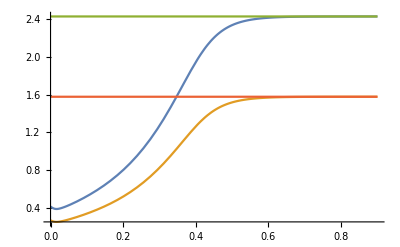
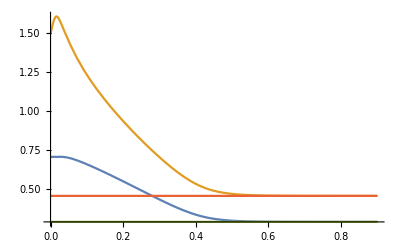
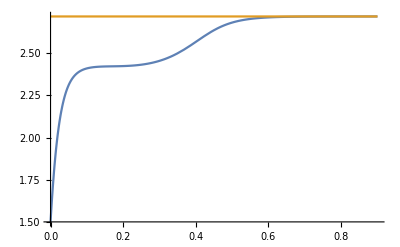
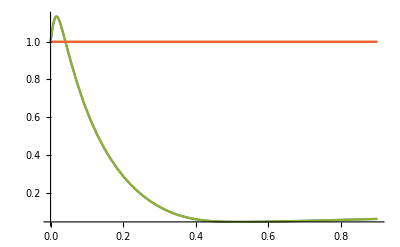

```mathematica
TMAX=0.9;
ICtable={0.1,0.01,1.2,1.,1.5,1,1};
eqsIC=Table[vars[[j]]-ICtable[[j]],{j,1,Length@vars}]/.tt->0;
ndsol=NDSolve[(eqsAssymSimpleWithCortexDensity/.repParamsAssym)~Join~eqsIC==Table[0,{i,1,2Length@vars}],varsSS,{tt,0,TMAX}]//Flatten;
vars/.tt->0/.ndsol
(eqsAssymSimpleWithCortexDensity/.repParamsAssym)/.ndsol/.tt->TMAX
{
Plot[{r[1][tt]/.ndsol,r[2][tt]/.ndsol,r[1]/.findroot,r[2]/.findroot},{tt,0,TMAX},PlotRange->All,ImageSize->400],
Plot[{α[1][tt]/.ndsol,α[2][tt]/.ndsol,α[1]/.findroot,α[2]/.findroot},{tt,0,TMAX},PlotRange->All,ImageSize->400],
Plot[{Δc[1][tt]/.ndsol,Δc[1]/.findroot},{tt,0,TMAX},PlotRange->All,ImageSize->400],
Plot[{ρ[1][tt]/.ndsol,ρ[1]/.findroot,ρ[2][tt]/.ndsol,ρ[2]/.findroot},{tt,0,TMAX},PlotRange->All,ImageSize->400]
}
```

```mathematica
tTable={0.1,0.25,0.4,0.8};
textTable=(Text[#] &)/@{"a","b","c","d"};
ptTable=Table[{ttt,r[1][ttt]/.ndsol},{ttt,tTable}];
pointTable=Table[Point[pt],{pt,ptTable}];
ptTable2=Table[{ttt,r[2][ttt]/.ndsol},{ttt,tTable}];
pointTable2=Table[Point[pt],{pt,ptTable2}];
offSetTable={{0,25},{-5,25},{-5,25},{0,25}};
labelTable=Table[Text[textTable[[ii]],Offset[offSetTable[[ii]],ptTable[[ii]]]],{ii,1,Length@ptTable}];
```

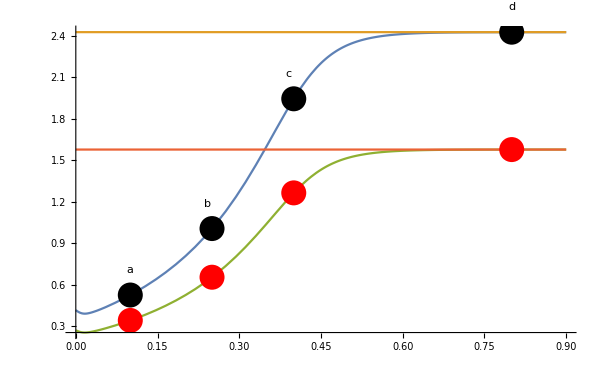

```mathematica
plot=Show[{Plot[{
r[1][tt]/.ndsol,r[1]/.findroot,
r[2][tt]/.ndsol,r[2]/.findroot
},{tt,0,TMAX},PlotRange->All]},
ImageSize->600,AspectRatio->2/(1+√5),
Epilog->{PointSize[0.03],pointTable,labelTable,Red,pointTable2} ]
```

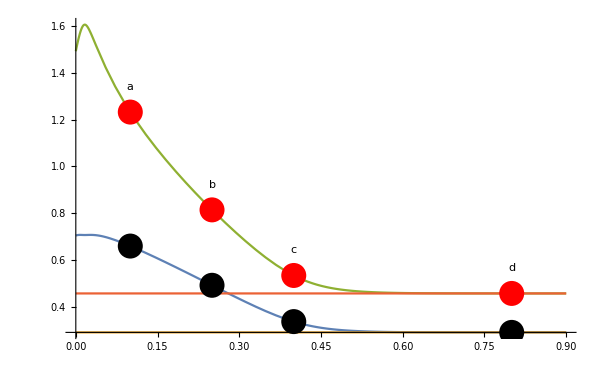

```mathematica
ptTable=Table[{ttt,α[1][ttt]/.ndsol},{ttt,tTable}];
pointTable=Table[Point[pt],{pt,ptTable}];
ptTable2=Table[{ttt,α[2][ttt]/.ndsol},{ttt,tTable}];
pointTable2=Table[Point[pt],{pt,ptTable2}];
offSetTable={{0,25},{0,25},{0,25},{0,25}};
labelTable=Table[Text[textTable[[ii]],Offset[offSetTable[[ii]],ptTable2[[ii]]]],{ii,1,Length@ptTable}];

plot=Show[{Plot[{α[1][tt]/.ndsol,α[1]/.findroot,α[2][tt]/.ndsol,α[2]/.findroot},{tt,0,TMAX},PlotRange->All]},
ImageSize->600,AspectRatio->2/(1+√5),
Epilog->{PointSize[0.03],pointTable,labelTable,Red,pointTable2} ]
```

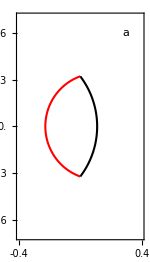
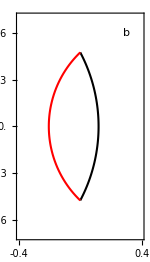
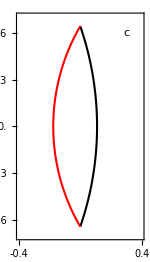
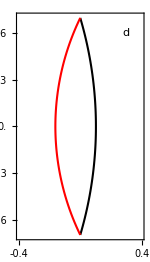

```mathematica
ticks={{Table[y,{y,-0.6,0.6,0.3}],None},{Table[x,{x,-0.4,0.4,0.4}],None}};
Table[
tt=tTable[[ii]];
paramPlot1=ParametricPlot[r[1][tt]{Cos[θ],Sin[θ]}-{r[1][tt]Cos[α[1][tt]],0}/.ndsol,{θ,-α[1][tt]/.ndsol,α[1][tt]/.ndsol},PlotStyle->{Thickness[0.01],Black}];
paramPlot2=ParametricPlot[-r[2][tt]{Cos[θ],Sin[θ]}+{r[2][tt]Cos[α[2][tt]],0}/.ndsol,{θ,-α[2][tt]/.ndsol,α[2][tt]/.ndsol},PlotStyle->{Thickness[0.01],Red}];
plotTable[ii]=Show[{paramPlot1,paramPlot2},
PlotRange->{{-0.4,0.4},{-0.7,0.7}},
ImageSize->150,
Frame->True,
FrameTicks->ticks,
BaseStyle->Directive[{FontFamily->"Latin Modern Math",FontSize->15,GrayLevel[0.3]}],
Epilog->Text[textTable[[ii]],{0.3,0.6}]
]
,{ii,1,Length@tTable}]
Clear[tt]
```

#### asymmetric actin turnover: example of lumen expansion + snapshots

```mathematica
Clear@tt
vars={r[1][tt],r[2][tt],α[1][tt],α[2][tt],Δc[1][tt],ρ[1][tt],ρ[2][tt]};
varsSS=vars/.f_[tt]->f
repParamsAssym={jw->0.02,jp->5,σσr->-0.16,γγj->1,jjPw->0.6,jjP->0.5,ccell[1]->0.01,ccell[2]->0.01,γ[1]->0.0002,γ[2]->0.0002,ν[1]->0.,ν[2]->0.4,β[1]->1,β[2]->5,ηb[1]->0.,ηb[2]->0.};
findroot=findSteadyStateAssymWithCortex[repParamsAssym]
```

{r[1],r[2],α[1],α[2],Δc[1],ρ[1],ρ[2]}

{{r[1]→1.17764,r[2]→1.17764,α[1]→0.672911,α[2]→0.672911,Δc[1]→2.71834,ρ[1]→1.,ρ[2]→1.}}

NDSolve::ivres: NDSolve has computed initial values that give a zero residual for the differential-algebraic system, but some components are different from those specified. If you need them to be satisfied, giving initial conditions for all dependent variables and their derivatives is recommended.

{0.671233,0.587349,0.741356,0.881559,1.5,1.,0.687576}

{-4.97146×10^-11,-2.1544×10^-10,6.33272×10^-15,2.48083×10^-11,-7.94298×10^-12,-3.01539×10^-9,-6.22456×10^-11}

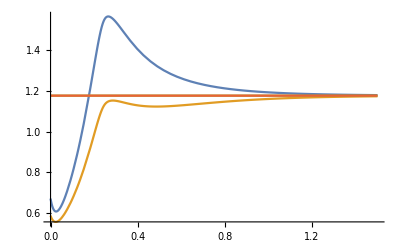
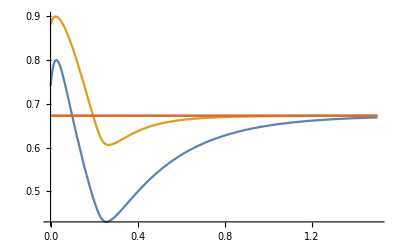
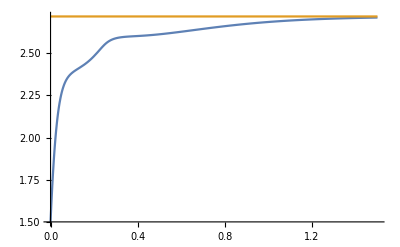
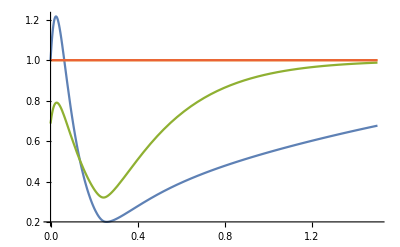

```mathematica
TMAX=1.5;
ICtable={0.5,0.5,0.6,0.6,1.5,1,0.7};
eqsIC=Table[vars[[j]]-ICtable[[j]],{j,1,Length@vars}]/.tt->0;
ndsol=NDSolve[(eqsAssymSimpleWithCortexDensity/.repParamsAssym)~Join~eqsIC==Table[0,{i,1,2Length@vars}],varsSS,{tt,0,TMAX}]//Flatten;
vars/.tt->0/.ndsol
(eqsAssymSimpleWithCortexDensity/.repParamsAssym)/.ndsol/.tt->TMAX
{
Plot[{r[1][tt]/.ndsol,r[2][tt]/.ndsol,r[1]/.findroot,r[2]/.findroot},{tt,0,TMAX},PlotRange->All,ImageSize->400],
Plot[{α[1][tt]/.ndsol,α[2][tt]/.ndsol,α[1]/.findroot,α[2]/.findroot},{tt,0,TMAX},PlotRange->All,ImageSize->400],
Plot[{Δc[1][tt]/.ndsol,Δc[1]/.findroot},{tt,0,TMAX},PlotRange->All,ImageSize->400],
Plot[{ρ[1][tt]/.ndsol,ρ[1]/.findroot,ρ[2][tt]/.ndsol,ρ[2]/.findroot},{tt,0,TMAX},PlotRange->All,ImageSize->400]
}
```

```mathematica
tTable={0.12,0.22,0.5,1.3};
textTable=(Text[#] &)/@{"a","b","c","d"};
ptTable=Table[{ttt,r[1][ttt]/.ndsol},{ttt,tTable}];
pointTable=Table[Point[pt],{pt,ptTable}];
ptTable2=Table[{ttt,r[2][ttt]/.ndsol},{ttt,tTable}];
pointTable2=Table[Point[pt],{pt,ptTable2}];
offSetTable={{-20,10},{-20,10},{0,25},{0,25}};
labelTable=Table[Text[textTable[[ii]],Offset[offSetTable[[ii]],ptTable[[ii]]]],{ii,1,Length@ptTable}];
```

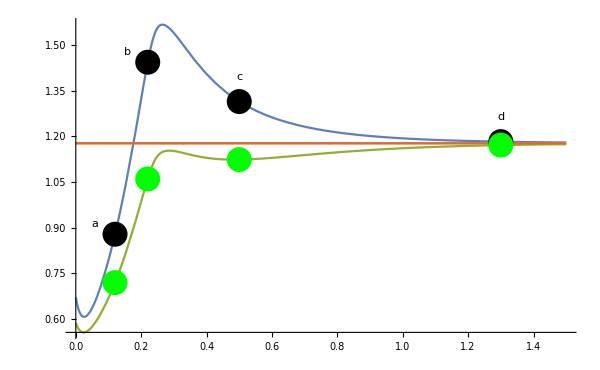

```mathematica
plot=Show[{Plot[{
r[1][tt]/.ndsol,r[1]/.findroot,
r[2][tt]/.ndsol,r[2]/.findroot
},{tt,0,TMAX},PlotRange->All]},
ImageSize->600,AspectRatio->2/(1+√5),
Epilog->{PointSize[0.03],pointTable,labelTable,Red,pointTable2}]
```

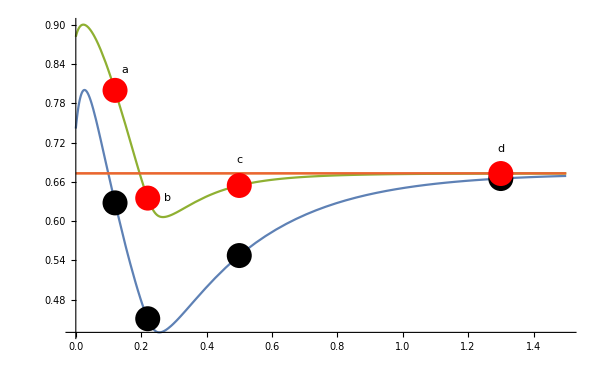

```mathematica
ptTable=Table[{ttt,α[1][ttt]/.ndsol},{ttt,tTable}];
pointTable=Table[Point[pt],{pt,ptTable}];
ptTable2=Table[{ttt,α[2][ttt]/.ndsol},{ttt,tTable}];
pointTable2=Table[Point[pt],{pt,ptTable2}];
offSetTable={{10,20},{20,0},{0,25},{0,25}};
labelTable=Table[Text[textTable[[ii]],Offset[offSetTable[[ii]],ptTable2[[ii]]]],{ii,1,Length@ptTable}];
plot=Show[{Plot[{α[1][tt]/.ndsol,α[1]/.findroot,α[2][tt]/.ndsol,α[2]/.findroot},{tt,0,TMAX},PlotRange->All]},
ImageSize->600,AspectRatio->2/(1+√5),
Epilog->{PointSize[0.03],pointTable,labelTable,Red,pointTable2} ]
```

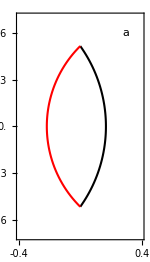
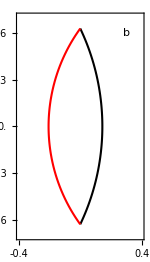
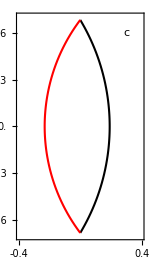
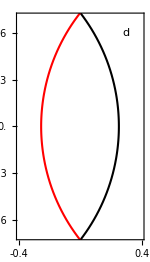

```mathematica
ticks={{Table[y,{y,-0.6,0.6,0.3}],None},{Table[x,{x,-0.4,0.4,0.4}],None}};
Table[
tt=tTable[[ii]];
paramPlot1=ParametricPlot[r[1][tt]{Cos[θ],Sin[θ]}-{r[1][tt]Cos[α[1][tt]],0}/.ndsol,{θ,-α[1][tt]/.ndsol,α[1][tt]/.ndsol},PlotStyle->{Thickness[0.01],Black}];
paramPlot2=ParametricPlot[-r[2][tt]{Cos[θ],Sin[θ]}+{r[2][tt]Cos[α[2][tt]],0}/.ndsol,{θ,-α[2][tt]/.ndsol,α[2][tt]/.ndsol},PlotStyle->{Thickness[0.01],Red}];
plotTable[ii]=Show[{paramPlot1,paramPlot2},
PlotRange->{{-0.4,0.4},{-0.7,0.7}},
ImageSize->150,
Frame->True,
FrameTicks->ticks,
BaseStyle->Directive[{FontFamily->"Latin Modern Math",FontSize->15,GrayLevel[0.3]}],
Epilog->Text[textTable[[ii]],{0.3,0.6}]
]
,{ii,1,Length@tTable}]
Clear[tt]
```